{a→5004.48,b→-77.6588,c→-0.414086}

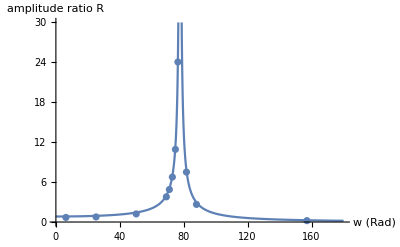

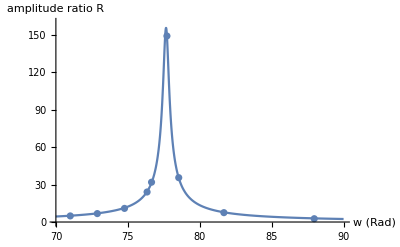

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

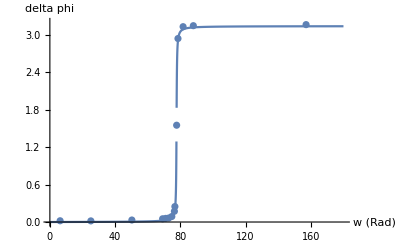

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

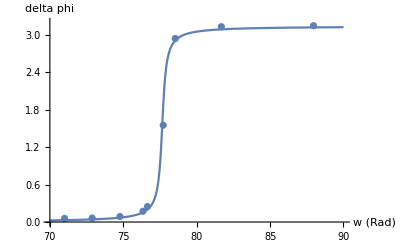

```mathematica
Clear[a,b,c,w];

AmpRatioData = {{6.28,0.687},{25.13,0.766},{50.27,1.218},{69.12,3.782},{71.00,4.883},{72.88,6.756},{74.77,10.918},{76.34,24.057},{76.65,31.915},{77.72,149.133},{78.54,35.561},{81.68,7.506},{87.96,2.646},{157.08,0.206}};
PhaseData = {{6.28,0.020},{25.13,0.018},{50.27,0.032},{69.12,0.052},{71.00,0.058},{72.88,0.064},{74.77,0.088},{76.34,0.172},{76.65,0.248},{77.72,1.552},{78.54,2.942},{81.68,3.132},{87.96,3.148},{157.08,3.165}};

FindFit[AmpRatioData,a/Sqrt[(w^2-b^2)^2+w^2 c^2],{a,b,c},w]

disp[w_]=a/Sqrt[(w^2-b^2)^2+w^2 c^2]/.%;

phi[w_]=Pi -Piecewise[{{Pi+ArcTan[c w/(b^2-w^2)],c w/(b^2-w^2)<0}},ArcTan[c w/(b^2-w^2)]]/.%%;

Show[Plot[disp[w],{w,0,180},PlotRange->{0,30}],ListPlot[AmpRatioData],AxesLabel->{"w (Rad)","amplitude ratio R"}]

Show[Plot[disp[w],{w,70,90},PlotRange->{0,160}],ListPlot[AmpRatioData],AxesLabel->{"w (Rad)","amplitude ratio R"}]

Show[Plot[phi[w],{w,0.1,180},PlotRange->{0,3.2}],ListPlot[PhaseData],AxesLabel->{"w (Rad)","delta phi"}] 

Show[Plot[phi[w],{w,70,90},PlotRange->{0,3.2}],ListPlot[PhaseData],AxesLabel->{"w (Rad)","delta phi"}]
```

```mathematica
{a->5004.476299840348,b->-77.65884982171099,c->-0.4140864238622939}
```

{a→5004.48,b→-77.6588,c→-0.414086}

```mathematica
nlm=NonlinearModelFit[AmpRatioData,a/Sqrt[(w^2-b^2)^2+w^2 c^2],{a,b,c},w];
Normal[nlm]
nlm["ParameterTable"]
```

5004.48/(√(0.171468 w^2+(-6030.9+w^2)^2))

| Estimate | Standard Error | t-Statistic | P-Value
a | 5004.48 | 25.9285 | 193.011 | 9.05741×10^-21
b | -77.6588 | 0.00540196 | -14376.1 | 2.31744×10^-41
c | -0.414086 | 0.0042347 | -97.784 | 1.59795×10^-17